# Solución HT1

## Ejercicio 1:

```mathematica
1)
```

```mathematica
Integrate[√Tan[x],x]
```

2/3 Hypergeometric2F1[3/4,1,7/4,-Tan[x]^2] Tan[x]^(3/2)

#### 2)

```mathematica
Integrate[Log[x+1]/(x^2+1),{x,0,1}]
```

1/8 π Log[2]

```mathematica
3)
```

```mathematica
Integrate[y/((x^2+y^2)^(3/2)),{y,-a,a}]
```

0

## Ejercicio 2:

```mathematica
1)
```

```mathematica
DSolve[{m*x'[t]==-m*g-b*x[t]},x[t],t]
```

{{x[t]→-9.8+ⅇ^(-1. t) C[1]}}

```mathematica
m=1
b=1
g=9.8
```

1

1

9.8

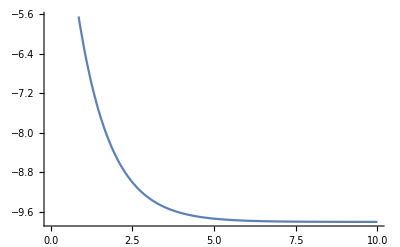

```mathematica
Plot[-9.8+9.8*ⅇ^(-1*t) ,{t,0,10}]
```

2)

```mathematica
DSolve[{x''[t]+9*x[t]==Sin[2*t],x[0]==2,x'[0]==0},x[t],t]
```

{{x[t]→1/30 (60 Cos[3 t]-5 Cos[3 t] Sin[t]-4 Sin[3 t]+5 Cos[t] Sin[3 t]-Cos[5 t] Sin[3 t]+Cos[3 t] Sin[5 t])}}

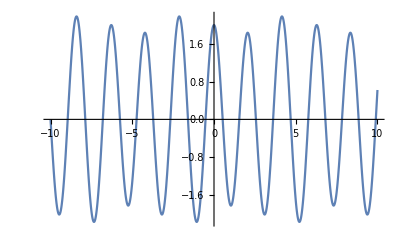

```mathematica
Plot[1/30*(60*Cos[3* t]-5*Cos[3*t]*Sin[t]-4 *Sin[3*t]+5*Cos[t]*Sin[3*t]-Cos[5*t]*Sin[3*t]+Cos[3*t]*Sin[5*t]),{t,-10,10}]
```

3)

```mathematica
{{solx,soly}}=DSolve[{x'[t]==5*x[t]+y[t],y'[t]==-2*x[t]+3*y[t],x[0]==1,y[0]==1},{x[t],y[t]},t]
```

{{x[t]→ⅇ^(4 t) (Cos[t]+2 Sin[t]),y[t]→ⅇ^(4 t) (Cos[t]-3 Sin[t])}}

```mathematica
x3[t_]:=x[t]/.solx
y3[t_]:=y[t]/.soly
```

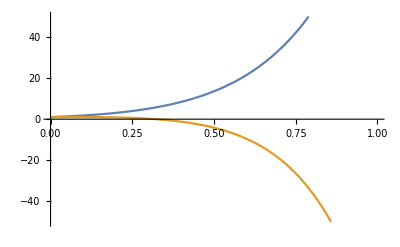

```mathematica
Plot[{x3[t],y3[t]},{t,0,10},PlotRange->{{0,1},{-50,50}}]
```

4)

```mathematica
{{solx4,soly4}}=DSolve[{x'[t]==-x[t]+3*y[t],y'[t]==-3*x[t]+5*y[t],x[0]==2,y[0]==3},{x[t],y[t]},t]
```

{{x[t]→ⅇ^(2 t) (2+3 t),y[t]→3 ⅇ^(2 t) (1+t)}}

```mathematica
x4[t_]:=x[t]/.solx4
y4[t_]:=y[t]/.soly4
```

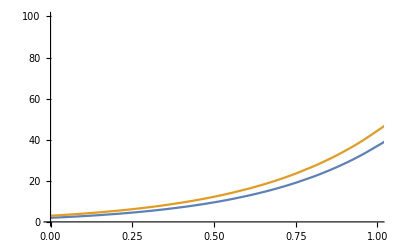

```mathematica
Plot[{x4[t],y4[t]},{t,0,10},PlotRange->{{0,1},{0,100}}]
```